```mathematica
complexNum = 3+ 2ⅈ;
```

```mathematica
Re[complexNum]
Im[complexNum]
```

3

2

```mathematica
seed = 1/4-ⅈ/3;
generate := Function[
{i},
If[i==0,seed,generate[i-1]^2+seed]
]
```

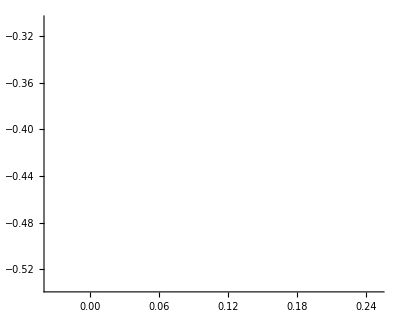

```mathematica
ComplexListPlot[Table[{generate[i]},{i,0,30}],Joined-> True]
```